```mathematica
coo=Import["~/Dropbox/FieldTrials/CRT/CoordSets/Coo1K.txt","Table"];
Dimensions[coo]
cooB=Table

cooB=Table[Join[coo[[i,{1,2}]],{If[coo[[i,4]]==3,"y","n"]},{coo[[i,3]]}],{i,Length[coo]}];
cooB[[1;;4]]
Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/C1kmFull.txt",cooB,"Table"];
c100=cooB[[1;;100]];
c1={cooB[[1]]};
Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/C1km100.txt",c100,"Table"];
Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/C1km1.txt",c1,"Table"];
```

{{-4.95063,12.1956,n,0.0347},{-4.9147,12.1956,n,0.0242},{-4.90572,12.1956,n,0.0729},{-4.88775,12.1956,n,0.0131}}

```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/GeneralMetapop/Run"];
pa=Flatten[{numruns=1,maxT=800,NumPat=4045,muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.5,eA=0.95,drivertime=100,NumDriver=1000,NumDriverPat=1,d=0.0005,Ld=0.15,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=500,al0var=0.,al1=10000,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=20,recsitesfreq=1,set=1,"e","r",start=700,"../InputData/C1kmFull.txt","../InputData/RainDailyAvAv.csv","none","../InputData/arab_mortality_Jan25.csv"}];

Export["Par"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""];
```

```mathematica
cout=Import["!./gdsimsapp<./Par"<>ToString[set]<>".csv","Table"];
tot=Import["./output_files/Totals1run1.txt","Table"];
```

{{Total,males,of,each,genotype},{Day,WW,WD,DD,WR,RR,DR},{0,5000000,0,0,0,0,0}}

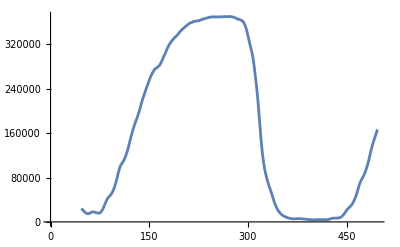

```mathematica
tot[[1;;3]]
ListLinePlot[tot[[50;;500,{1,2}]]]
```

```mathematica
loc=Partition[Drop[Import["./output_files/LocalData1run1.txt","Table"],2],NumPat];
Dimensions[loc]
```

{41,100,8}

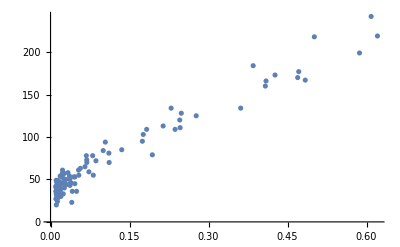

```mathematica
ListPlot[Transpose[{c100[[All,4]],loc[[41,All,3]]}]]
```

```mathematica
loc[[26,All,3]]
```

{1774,1794,1803,1637,1459,1806,1665,1794,1799,1681,1711,1674,1948,1729,1698,1808,1779,1874,2149,1892,1872,1707,2000,1855,1737,1858,1685,1891,1909,1782,1661,1676,1915,2051,2035,1739,1832,1542,1722,1751,1781,1934,2203,2076,2018,1885,1740,1681,1737,1841,1752,1685,1841,1723,1523,1877,2085,2113,1855,1594,1660,1689,1933,2075,2233,2007,1700,1519,1847,1867,1769,1608,1839,2046,2067,1707,1470,1722,1506,1609,1671,1643,1696,1688,1784,1691,1854,1912,1900,1633,1677,1684,1585,1840,1675,1626,2072,1997,1692,1768}

{365,1}

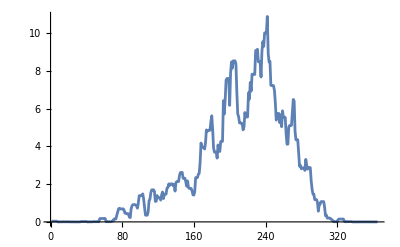

```mathematica
rain=Import["../InputData/RainDailyAvAv.csv","Table"];
Dimensions[rain]
ListLinePlot[rain[[All,1]]]
```